# Main model execution document

```mathematica
SetDirectory[NotebookDirectory[]]
ClearAll[t]
```

/home/eric/git/MCMICM2017/MMAmodel

## Document stocks + stuff with initial conditions

[[SOURCE]] -> lake1inflow -> lake1 -> lake1outflow -> [[SINK]]

```mathematica
initialConds={lake1Vol[0]==2.6239857119877324*^12};
behaviors={lake1Vol'[t]==lake1inflow[t]-lake1outflow[t]};
```

## Define lake properties

These convert volume in m^3 into height in meters

```mathematica
With[{surfacearea =N@QuantityMagnitude[UnitConvert[ Quantity[2085, ("Miles")^2],"m^2"]]},
lakeEqns={lake1Height[t]==lake1Vol[t]/surfacearea}];
```

```mathematica
Solve[lakeEqns,lake1Vol[t]];
First[lake1Vol[t]/.%/.lake1Height[t]->height20112012[DateObject[{2000, 10,10}]]]
```

2.62399×10^12

## Define source inflow

```mathematica
zambeziFraction = 0.77;
```

Sun 1 Oct 2000

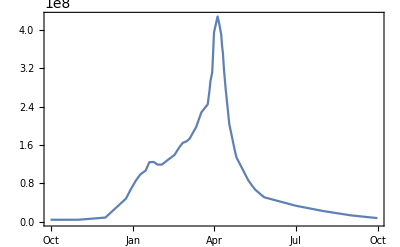

```mathematica
flow20112012=TimeSeries@Import["../Data/Data 2/Pink Line.csv","Data"];
flow20112012=TimeSeriesMap[#*QuantityMagnitude@UnitConvert[Quantity[1, "Days"], "Seconds"]/zambeziFraction&,flow20112012];
startDate=flow20112012["Dates"][[1]]
DateListPlot[flow20112012]
```

```mathematica
inflows={lake1inflow[t]==flow20112012[startDate+Quantity[t, "Days"]]};
```

## Define dam policies

```mathematica
damOutflow[t_]:=80000000
zambeziOutflowFraction = 0.86
damPolicy={lake1outflow[t]==damOutflow[t]/zambeziOutflowFraction};(* m^3/day *)
```

0.86

## Run simulation

```mathematica
sol=NDSolveValue[{initialConds,behaviors,lakeEqns,inflows,damPolicy},lake1Height[t],{t,0,364}]
```

InterpolatingFunction[{{0., 364.}}, <>][t]

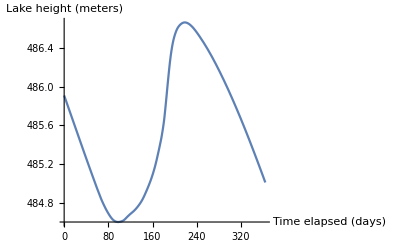

```mathematica
With[{tmin=sol[[0]]["Domain"][[1,1]],tmax=sol[[0]]["Domain"][[1,2]]},
Plot[sol,{t,tmin,tmax},AxesLabel->{"Time elapsed (days)","Lake height (meters)"},ImageSize->Full]
]
```

## Height Data

```mathematica
height20112012=TimeSeries@RotateLeft[Import["../Data/Data 1/Yellow Line.csv","Data"],31];
```

AbsoluteTime::ambig: Warning: the interpretation of the string 1/2/2001 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 1/4/2001 as a date is ambiguous.

AbsoluteTime::ambig: Warning: the interpretation of the string 1/7/2001 as a date is ambiguous.

General::stop: Further output of AbsoluteTime::ambig will be suppressed during this calculation.

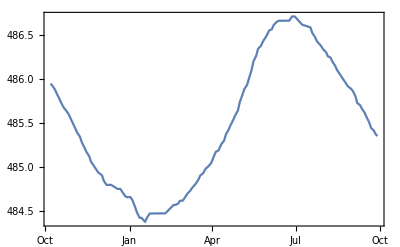

```mathematica
DateListPlot[height20112012]
```

```mathematica
height20112012["Values"][[1]]
```

485.951

```mathematica
RotateLeft[Import["../Data/Data 1/Yellow Line.csv","Data"],31];
```

## Bath

```mathematica
b`raw=Import["../Data/Bathymetry.asc","Data"];
b`d=ToExpression/@StringSplit[b`raw[[8;;]]];
b`h=AssociationThread@@MapAt[ToExpression,Transpose@StringSplit@b`raw[[;;7]],2];
ArrayPlot[b`d, ImageSize->Full]
GeoGraphics[GeoBoundsRegion[{
{b`h[["yllcorner"]],b`h[["yllcorner"]]+(b`h[["dy"]]*b`h[["nrows"]])},
{b`h[["xllcorner"]],b`h[["xllcorner"]]+(b`h[["dx"]]*b`h[["ncols"]])}
}]]
```

-Graphics-

-Graphics-

```mathematica
ListPlot3D[b`d,MeshFunctions->{#3&},Mesh->40,DataRange->{{b`h[["yllcorner"]],b`h[["yllcorner"]]+(b`h[["dy"]]*b`h[["nrows"]])},
{b`h[["xllcorner"]],b`h[["xllcorner"]]+(b`h[["dx"]]*b`h[["ncols"]])}},AspectRatio->b`h[["nrows"]]/b`h[["ncols"]]]
```

-Graphics3D-